0.777778

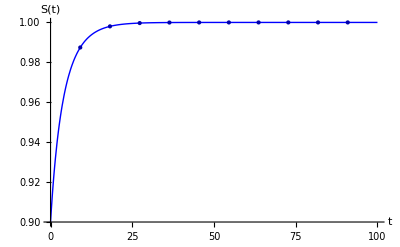

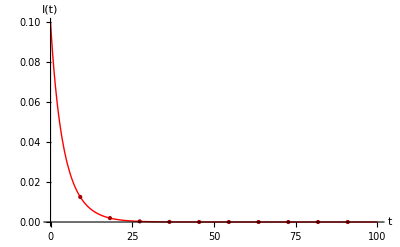

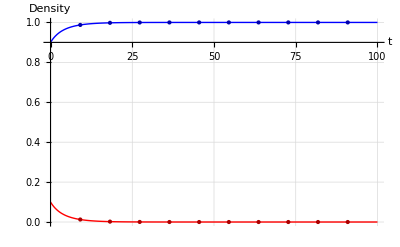

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]*i[t]/n+γ*i[t];
eq2=β*s[t]*i[t]/n-γ*i[t];
n=1;
β=0.7;
γ=0.9;
R0=N[β/γ]
tf=100;
szero=0.90;
izero=0.1;


sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,s[0]==szero,i[0]==izero},{s,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


ShowLegend[Show[plot1a ,plot2a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.2},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

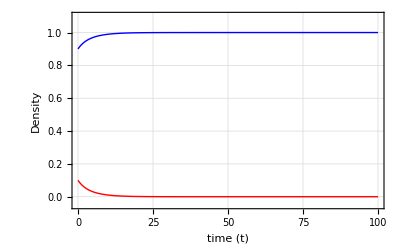

1.

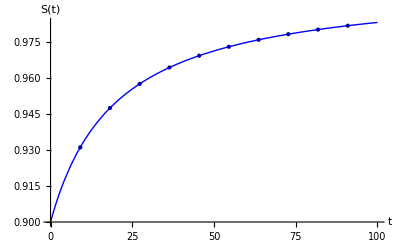

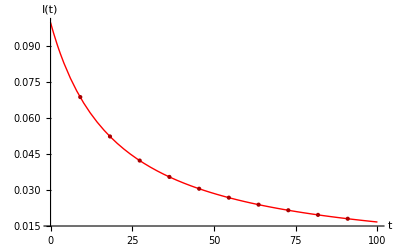

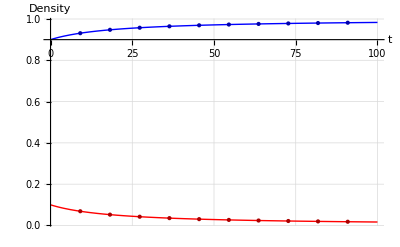

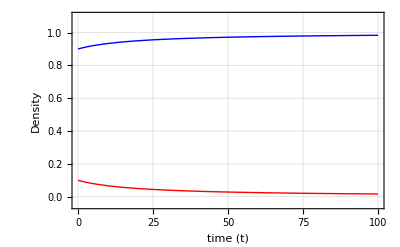

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]*i[t]/n+γ*i[t];
eq2=β*s[t]*i[t]/n-γ*i[t];
n=1;
β=0.5;
γ=0.5;
R0=N[β/γ]
tf=100;
szero=0.90;
izero=0.1;


sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,s[0]==szero,i[0]==izero},{s,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


ShowLegend[Show[plot1a ,plot2a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.2},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

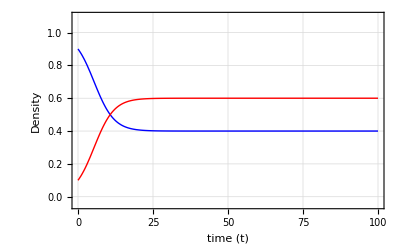

```mathematica
max = 0.0;
arrow=Graphics[{Arrowheads[0.03],Arrow[{{2,0.1},{1,0}}]}];
aa=Plot[Piecewise[{{0,r0<1},{(1-1/r0)*1,r0>1}}],{r0,0,10},PlotRange->{{0,10},{-0.1,1.1}},PlotStyle->{Thick, Magenta},GridLines->{{},{max}},GridLinesStyle-> Directive[Dashed, Gray],Frame->{True,True,True,True},FrameLabel->{{"Infected Fraction, I(t)",""},{"Basic Reproduction Ratio (R_0)",""}}];
Show[{aa,arrow}]
```

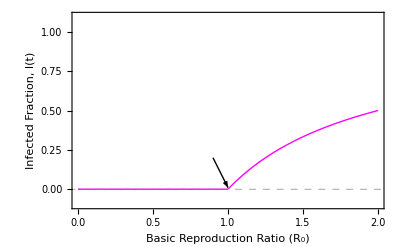

```mathematica
min=0;
max = 1.0;
n=1;
c=1.5;
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.9,0.2},{0.9999,0.01}}]}];
aa1=Plot[Piecewise[{{0,r0<1},{(1-1/r0)*1,r0>1}}],{r0,0,2},PlotRange->{{0.0,2},{-0.1,1.1}},PlotStyle->{Thick, Magenta},GridLines->{{},{min}},GridLinesStyle-> Directive[Dashed, Gray],Frame->{True,True,True,True},FrameLabel->{{"Infected Fraction, I(t)",""},{"Basic Reproduction Ratio (R_0)",""}}];

Show[{aa1,arrow}]
```

```mathematica
(*This is example of Tunnel Diode Example*)Clear["Global`*"]

eq1=γ *i[t]-β * s[t]*i[t]/n;
eq2=β*s[t]*i[t]/n-γ*i[t];
(*eq3=γ*i[t]-μ r[t];*)
n=1;
μ=0.6;
β=0.5;
γ=0.4;
R0=N[β/(γ+μ)]
St=n/R0
It=(n μ (R0-1))/β
tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3, s[0]==szero[k],i[0]==izero[k],r[0]==rzero[k]},{s,i,r},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
Show[pls,line,arrow,PlotRange->{{0.0,1.01},{-0.01,1.0}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (I)",""},{"Susceptible "[S],""}}]
```

```mathematica
Clear["Global`*"]
β=0.05;
γ=0.02;
r0=β/γ

e1={1,0};
e2={1/r0, (1-1/r0)};
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=1;
VectorPlot[{-β s i/1+γ i, β s i/1-γ i},{s,e1[[1]]-δ,e1[[1]]},{i,e1[[2]]-0.02,e1[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

2.5

```mathematica
Clear["Global`*"]
β=0.7;
γ=0.9;
r0=β/γ

e1={1,0};
e2={1/r0, (1-1/r0)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=1.3;
VectorPlot[{-β s i/1+γ i, β s i/1-γ i},{s,e2[[1]]-1.0,e2[[1]]+0.2},{i,e2[[2]]+0.25,e2[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

0.777778

{1.28571,-0.285714}